```mathematica
WebImageSearch["Resistor", "Thumbnails"]
```

$Aborted

```mathematica
ColorQuantize[-Graphics-,14]
```

-Graphics-

```mathematica
ColorQuantize[ColorConvert[-Graphics-,"CMYK"],14]
```

-Graphics-

```mathematica
Map[ColorQuantize[#,14]&,WebImageSearch["Resistor", "Thumbnails"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pictures = WebImageSearch["resistor","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
img = -Graphics-;
saturated = Binarize[ColorConvert[img, "Grayscale"], .9]
Inpaint[img, Dilation[saturated, DiskMatrix[20]]]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[a]
```

```mathematica
ColorQuantize[-Graphics-, 10]
```

-Graphics-

```mathematica
MorphologicalComponents[-Graphics-]//Colorize
```

-Graphics-

```mathematica
lenet=NetChain[
{
ConvolutionLayer[20,5],
Ramp,
PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
500,
Ramp,
10,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

```mathematica
ImageIdentify[-Graphics-]
```

resistor

```mathematica
Entity["Concept","Resistor::d7w57"]["Properties"]
```

{alternate names,broader concepts,definition,equivalent entity,name,narrower concepts,similar entities,subset concepts,superset concepts,WordData senses,WordNet ID}

```mathematica
ImageAlign[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
WebImageSearch["Resistor","Images","MaxItems"->1]
```

{-Graphics-}

```mathematica
DeleteSmallComponents @ChanVeseBinarize[-Graphics-]
```

-Graphics-

```mathematica
HistogramTransform @ ImageAdjust[-Graphics-]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

-Graphics-

```mathematica
ColorQuantize[ImageAdjust[-Graphics-,1],14]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
CrossingDetect[-Graphics-]
```

-Graphics-

```mathematica
ContourDetect[-Graphics-]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
GradientFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
LaplacianGaussianFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = EdgeDetect[-Graphics-]
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

-Graphics-

```mathematica
Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]
```

Massachusetts, United States

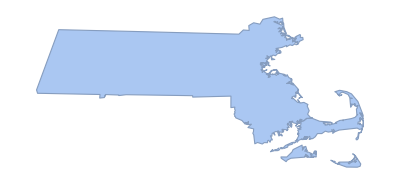

```mathematica
BoundaryDiscretizeGraphics[Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]]
```

## From article

```mathematica
img = RemoveAlphaChannel[-Graphics-];
img = ImageResize[img, {600}];
img = ColorConvert[RemoveAlphaChannel[img],"RGB"];
```

```mathematica
edge = ImageCrop[img,{10,10},{Right,Bottom}]
backColor = RGBColor [Mean @ Catenate[ImageData[edge]]]
```

-Graphics-

RGBColor[{0.43039215686274473, 0.9200784313725486, 0.9057254901960783}]

```mathematica
substracted = ImageApply[
	MapThread[
		Abs[#1 - #2]&,
		{Flatten[#],Flatten[List @@ backColor]}
	]&,
	img
]
```

-Graphics-

```mathematica
monochromatic = ColorConvert[substracted,"Grayscale"]
```

-Graphics-

```mathematica
threshold[n_] := Module[
	{num, p, ω, μ, μT, maxK, maxσ, σ2B, temp, k},
	num = Total[n];
	p = n / num;
	ω := Sum[p[i],{i,0,#}]&;
	μ := Sum[(i+1) * p[i], {i, 0, #}]&;
	μT = μ[255];
	σ2B[x_Integer] := Module[
		{μk, ωk},
		ωk = ω[x];
		μk = μ[x];
		If[ ωk ≠ 0 && ωk ≠ 1,
			((μT*ωk - μk)^2) / (ωk * (1 - ωk)),
			-1
		]
	];
	maxσ = 0;
	maxK = 255;
	For[k = 0, k < 255, k++,
		temp = σ2B[k];
		If[ NumberQ[temp] && temp > maxσ,
			maxσ = temp;
			maxK = k;
		]
	];
	maxK
]
```

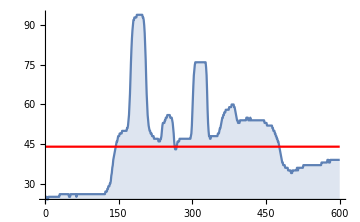
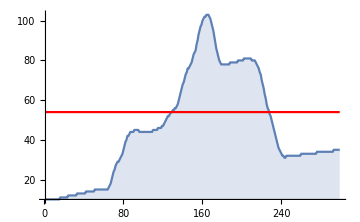
-Graphics- | -Graphics-
Horizontal mean | Vertical mean

```mathematica
matr = ImageData[monochromatic];
verMean = Map[
	Mean[Flatten[#]]&,
	matr
];
verMean = Round[verMean * 255];
horMean = Map[
	Mean[Flatten[#]]&,
	Transpose[matr]
];
horMean = Round[horMean * 255];

horFrequency = Counts[Catenate[{horMean,Range[0,255]}]] - 1;
verFrequency = Counts[Catenate[{verMean,Range[0,255]}]] - 1;
verThreshold = threshold[verFrequency];
horThreshold = threshold[horFrequency];

verPlot = DiscretePlot[
	verMean[[x]],
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium
];
verThresholdPlot = Plot[
	verThreshold,
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

horPlot = DiscretePlot[
	horMean[[x]],
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium
];
horThresholdPlot = Plot[
	horThreshold,
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

Grid[{
	{Show[{horPlot, horThresholdPlot}], Show[{verPlot, verThresholdPlot}]},
	{"Horizontal mean", "Vertical mean"}
}]
```

## Clustering the colors

```mathematica
extracted = ColorConvert[ImageCrop[img, {350, 15}],"LUV"]
```

-Graphics-

```mathematica
DominantColors[extracted]
```

{RGBColor[0.9623737559079278, 0.7256759384369725, 0.5338557906501769],RGBColor[0.650920666454433, 0.4770286203892075, 0.21433296590351414],RGBColor[0.9804521929360984, 0.28438310891253055, 0.16009693223803537],RGBColor[0.13260671973813978, 0.12853713208351086, 0.12027019392867577],RGBColor[0.18054232858410646, 0.3735820134359856, 0.6310006481145575],RGBColor[0.5914845847337749, 0.5514966939361491, 0.5842396413595597]}

```mathematica
.10DominantColors[extracted]
```

.10DominantColors[-Graphics-]

```mathematica
ClusteringComponents[extracted,5,CriterionFunction->"StandardDeviation"]//Colorize
```

-Graphics-

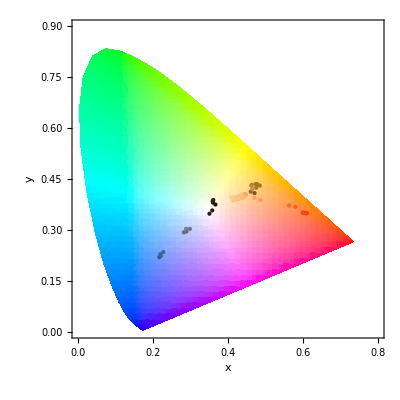

```mathematica
ChromaticityPlot[extracted]
```

## Dividing the image in sections

```mathematica
mask = Binarize[substracted]
```

-Graphics-

```mathematica
PixelValuePositions[mask, Black]
```

{{1,299},{2,299},{3,299},{4,299},{5,299},{6,299},{7,299},{8,299},{9,299},{10,299},{11,299},{12,299},{13,299},{14,299},{15,299},136269,{586,1},{587,1},{588,1},{589,1},{590,1},{591,1},{592,1},{593,1},{594,1},{595,1},{596,1},{597,1},{598,1},{599,1},{600,1}}
 |  |  |  |

```mathematica
meanColorMask[image_,mask_ ]:= Module[
{toRemove,imgList},
toRemove = PixelValuePositions[mask, Black];
imgList = Transpose @ ImageData[image];
imgList = Delete[imgList, toRemove];
RGBColor[Mean[Catenate @ imgList]]
]
```

```mathematica
maskColumns =First @ ImagePartition[mask, {10, ImageData[img][[1]]//Length}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
columns =First @ ImagePartition[img,{10, ImageData[img][[1]]//Length}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[meanColorMask[columns[[x]],maskColumns[[x]]],{x,Length[columns]}]
```

{RGBColor[{0.34360194945030037, 0.8639918395103706, 0.819766519324493}],RGBColor[{0.36227106227106254, 0.8638655462184865, 0.8187890540831715}],RGBColor[{0.3807084123972172, 0.86662449926207, 0.818026565464895}],RGBColor[{0.3770278637770899, 0.8593395252837972, 0.8115170278637764}],RGBColor[{0.3786996904024768, 0.8571929824561398, 0.8091021671826619}],RGBColor[{0.39154870504351463, 0.8550068155604486, 0.8069833280905935}],RGBColor[{0.40564270152505444, 0.8528976034858391, 0.8071677559912848}],RGBColor[{0.4135647701703633, 0.8510232508303862, 0.80053573341905}],RGBColor[{0.4424767801857584, 0.8476986584107322, 0.8022084623323007}],RGBColor[{0.45255300089578965, 0.8440927640091562, 0.8003583159151982}],RGBColor[{0.5658053875755911, 0.8674179952354758, 0.8051493494594087}],RGBColor[{0.6523944193061845, 0.8904223227752625, 0.7909313725490191}],RGBColor[{0.833442622950819, 0.8351398264223713, 0.6973320475731272}],RGBColor[{0.9564058633162018, 0.814513611269751, 0.6654254711593364}],RGBColor[{0.964879285047355, 0.8464585834333698, 0.6994531145791653}],RGBColor[{0.955817753457976, 0.8273559811521466, 0.6610807113543088}],RGBColor[{0.959538552263014, 0.8329057938965021, 0.653807312398645}],RGBColor[{0.9312729831269074, 0.5065514357401715, 0.34217743969625913}],RGBColor[{0.9301905486048782, 0.33595769682726234, 0.22794405658855915}],RGBColor[{0.9348590222344123, 0.3363002044149054, 0.2337364532300993}],RGBColor[{0.9329292313166436, 0.5313865273912551, 0.3857039380885214}],RGBColor[{0.9621946680770247, 0.863426769309117, 0.7007737360678536}],RGBColor[{0.9582959454968468, 0.8861831173147168, 0.737200897308074}],RGBColor[{0.7218648310387968, 0.7276512307050443, 0.7315853149770529}],RGBColor[{0.33355788123020197, 0.5408356389590585, 0.7655599663178123}],RGBColor[{0.30864357779219986, 0.5149566346097116, 0.7479221979664438}],RGBColor[{0.7783417235592951, 0.7604073282302348, 0.7512953129669194}],RGBColor[{0.9607579354611844, 0.8376373867932803, 0.6740877516926038}],RGBColor[{0.9601553010584802, 0.8323442651396814, 0.6640985597778928}],RGBColor[{0.9164659146432168, 0.7924075372294085, 0.6315509952626761}],RGBColor[{0.3239794036500994, 0.29846707682320595, 0.26249723365644345}],RGBColor[{0.22414565826330715, 0.24953501400560438, 0.24507563025210227}],RGBColor[{0.2645232533446593, 0.26404473702838616, 0.2462716783464292}],RGBColor[{0.8462634853138057, 0.7229860618946358, 0.5806598944798802}],RGBColor[{0.966024795568455, 0.8347006067000775, 0.6739162929745889}],RGBColor[{0.9048558482697793, 0.7702313645294497, 0.5903725089217697}],RGBColor[{0.7335280913712275, 0.6024658348187755, 0.37314319667260853}],RGBColor[{0.6917082442385343, 0.5615893114195083, 0.32392771791539066}],RGBColor[{0.7684729207668222, 0.619549529849115, 0.38594358189372463}],RGBColor[{0.9589964315932787, 0.8154912997093746, 0.6307361218408564}],RGBColor[{0.9666703316840782, 0.8309620670698166, 0.6690709180868603}],RGBColor[{0.9639561166547231, 0.8282522005990728, 0.6601576713159475}],RGBColor[{0.9710342994894029, 0.8350625438946109, 0.6593512138640549}],RGBColor[{0.9713729308666041, 0.8391316799358449, 0.6683047902705384}],RGBColor[{0.9739538196711611, 0.8471498387447747, 0.6736867097999638}],RGBColor[{0.9790083197458124, 0.8739370375015645, 0.7157949747063008}],RGBColor[{0.9831309588055446, 0.8761962583198362, 0.7233495232955589}],RGBColor[{0.986228192064233, 0.8592249498224495, 0.7001018990273273}],RGBColor[{0.9401617250673866, 0.8367528143332801, 0.6982611912689597}],RGBColor[{0.8372135352031121, 0.8685198974104398, 0.7372052618515764}],RGBColor[{0.7296806722689071, 0.8655910364145648, 0.7779271708683473}],RGBColor[{0.6151802656546488, 0.813620071684587, 0.7639679527725061}],RGBColor[{0.5706778142729168, 0.7775853488603558, 0.7334328655319985}],RGBColor[{0.6335205438959505, 0.8097546556310963, 0.7628337767267709}],RGBColor[{0.6933746130030954, 0.8270175438596484, 0.77486068111455}],RGBColor[{0.7042105263157885, 0.834984520123837, 0.7707120743034048}],RGBColor[{0.6879976232917401, 0.8159437512378673, 0.759675183204594}],RGBColor[{0.6767617938264411, 0.7950495049504938, 0.7450203843913797}],RGBColor[{0.6913602941176462, 0.7889093137254898, 0.7406454248366008}],RGBColor[{0.693901960784313, 0.7867058823529404, 0.7421960784313723}]}

```mathematica
resistorBackColor = meanColorMask[img, mask]
```

RGBColor[{0.7861002269633819, 0.6781417655109769, 0.5628677010814515}]

```mathematica
Table[RGBColor @ Mean[Catenate[ImageData[columns[[x]]]]],{x,Length[columns]}]
```

{RGBColor[{0.3484621942422474, 0.8470614466522418, 0.8058469407830181}],RGBColor[{0.34401993573349343, 0.8450442651977214, 0.8027096858810547}],RGBColor[{0.3416105974162285, 0.8441917502787116, 0.8015935471178584}],RGBColor[{0.3381152862482843, 0.843113646796512, 0.8004131418453824}],RGBColor[{0.3395160338382898, 0.8436435176077134, 0.8008380877434753}],RGBColor[{0.34067283100531864, 0.8455164273067133, 0.7994583251360906}],RGBColor[{0.3421680110171244, 0.8464633746475217, 0.8002177191947186}],RGBColor[{0.3382425077054327, 0.84402124729491, 0.7975093448750882}],RGBColor[{0.33537805757755407, 0.8436422060463019, 0.7968456947996742}],RGBColor[{0.33587251623057984, 0.8404446193193011, 0.7947734277657685}],RGBColor[{0.3452934618663603, 0.8439241917502862, 0.7922119483244947}],RGBColor[{0.37244278313332924, 0.8541806020066994, 0.7935707259492595}],RGBColor[{0.4164233720244051, 0.8533871073513134, 0.7861341727326587}],RGBColor[{0.521482064397674, 0.8437327037838648, 0.7610217063414172}],RGBColor[{0.5928847793298061, 0.8063322185061401, 0.7069932454587203}],RGBColor[{0.6105410190832327, 0.7862036854875787, 0.6770529215030355}],RGBColor[{0.6244658666142135, 0.7817522460489278, 0.6659177650993375}],RGBColor[{0.657240474785245, 0.6493907797232477, 0.5367932323430944}],RGBColor[{0.6790268214309214, 0.5559302249327824, 0.47406518460226027}],RGBColor[{0.6851688635320433, 0.5543235622008004, 0.47354318315954386}],RGBColor[{0.6702695258705582, 0.668763853367419, 0.5634297330972438}],RGBColor[{0.6384143222506533, 0.7942055216735605, 0.6809758016919096}],RGBColor[{0.6338264804249562, 0.8097737556561155, 0.7000629549478714}],RGBColor[{0.48472949045839686, 0.7380247885107117, 0.71070102957571}],RGBColor[{0.29442586399108545, 0.6630585612170995, 0.7417456882418649}],RGBColor[{0.2875270509541631, 0.663475637746709, 0.7400629549478747}],RGBColor[{0.47549085185914347, 0.7539418978293586, 0.7249183553019911}],RGBColor[{0.5703770739064892, 0.7926211554856093, 0.6918525804970717}],RGBColor[{0.5706997180143, 0.7916178110040036, 0.6886667978227983}],RGBColor[{0.5422388353334672, 0.7712322119483231, 0.6730120007869302}],RGBColor[{0.30991802741164, 0.5932074234375769, 0.5494681618466785}],RGBColor[{0.2636369598006519, 0.5716361728637724, 0.5429313397599836}],RGBColor[{0.28259426847662883, 0.5791671585021767, 0.5439950160666275}],RGBColor[{0.5264397665420721, 0.7609351432880824, 0.6675572168666715}],RGBColor[{0.5622375237720587, 0.789179618335634, 0.686835858089048}],RGBColor[{0.5331746344022661, 0.7622886746671849, 0.651301724703258}],RGBColor[{0.48036854875731105, 0.7084792445406058, 0.5729516689619101}],RGBColor[{0.4814361597481967, 0.6988733687454719, 0.5544219293068432}],RGBColor[{0.5235648239228885, 0.715686274509793, 0.5714682930028251}],RGBColor[{0.5974227818217647, 0.7685920388222236, 0.6491389599317905}],RGBColor[{0.6054272411305771, 0.7707259492425815, 0.6596091546986558}],RGBColor[{0.6044724244212857, 0.76774477014887, 0.6537910682667561}],RGBColor[{0.6031674208144914, 0.7698144140599431, 0.6528100203291901}],RGBColor[{0.601343038887807, 0.7720361990950284, 0.6562515574791663}],RGBColor[{0.6010859728506907, 0.7769637353269121, 0.6606046298117851}],RGBColor[{0.5991920781690753, 0.7914236999147569, 0.6780523313004082}],RGBColor[{0.5890720702997049, 0.8009535051478872, 0.6901265656764436}],RGBColor[{0.5549531116794707, 0.8232867729031559, 0.7219279952783842}],RGBColor[{0.42400026231229504, 0.8325923011345189, 0.7536284346514596}],RGBColor[{0.337593284805579, 0.83514328808448, 0.7607869368483244}],RGBColor[{0.29109056331564725, 0.8268043806151302, 0.761394189782944}],RGBColor[{0.26779198635978146, 0.8167892976588692, 0.7584221916191283}],RGBColor[{0.2618178241196356, 0.8112138500885387, 0.7538435307233322}],RGBColor[{0.261968653682231, 0.8121896517804527, 0.7561859794084914}],RGBColor[{0.2642861827005264, 0.8131759459636785, 0.7557964456685736}],RGBColor[{0.2638284477670887, 0.8122670339038733, 0.7535287559840048}],RGBColor[{0.25783592366714675, 0.8089094366843816, 0.7503665814151744}],RGBColor[{0.2550960718735863, 0.8056462718866891, 0.7490327234572701}],RGBColor[{0.2534749819660523, 0.8041287953308498, 0.7477801823070214}],RGBColor[{0.2522880188865066, 0.8028224801626421, 0.7473552364089335}]}

```mathematica
meanColorMask[img, mask]
```

RGBColor[{0.7861002269633819, 0.6781417655109769, 0.5628677010814515}]

```mathematica
Map[DominantColors[ImageResize[#,{1,5}]]&,columns]
```

{{RGBColor[0.25506359556312813, 0.8313521645805483, 0.7783946453389483]},{RGBColor[0.25072879441906143, 0.8293835246467532, 0.778393220821886]},{RGBColor[0.2467940439869336, 0.8293847699004273, 0.7764396604194371]},{RGBColor[0.24515992350554577, 0.8274187937595299, 0.7764399399372698]},{RGBColor[0.23947308853548027, 0.8293881283446995, 0.7744860169787755]},{RGBColor[0.24005062648456366, 0.8293908715723187, 0.7744857932692772]},{RGBColor[0.23783588981521625, 0.8293873690672179, 0.7725177824667381]},{RGBColor[0.2316785522723122, 0.8293872940571985, 0.7705643905447402]},{RGBColor[0.2294805932472046, 0.8333059244582691, 0.7685962854697221]},{RGBColor[0.2312670393843096, 0.8313362898236174, 0.7705492494356248]},{RGBColor[0.2339763991956202, 0.8333066859080522, 0.7705497657844789]},{RGBColor[0.24144941664412717, 0.8352770297896824, 0.7725061946121957]},{RGBColor[0.3811208608728641, 0.9039389235418454, 0.874489634929246]},{RGBColor[0.49019546386563, 0.7803920455721141, 0.6823522908071978],RGBColor[0.18430897762715664, 0.8549019702649737, 0.7960776045898402]},{RGBColor[0.20783893675497322, 0.8588235314452588, 0.7999991662771766]},{RGBColor[0.21960399587318385, 0.8509803875087528, 0.7882344701130486]},{RGBColor[0.22352581485825196, 0.8431372791699032, 0.7843129356726013]},{RGBColor[0.23529082160761344, 0.8392157318125933, 0.776469832047342]},{RGBColor[0.831373536929173, 0.2078404359043875, 0.1098046476982126],RGBColor[0.24313414536044453, 0.8274509681744195, 0.7686266491915484]},{RGBColor[0.8509814136841566, 0.21176189889795455, 0.10980469552623981],RGBColor[0.2509775128113787, 0.8274510179374838, 0.76470513544195]},{RGBColor[0.788236184232317, 0.3647046580235919, 0.23921576192801064],RGBColor[0.24313420153653387, 0.8313725714153081, 0.76470512136786]},{RGBColor[0.23136919964863145, 0.8352941211663699, 0.7725482263042217]},{RGBColor[0.2235257803234334, 0.8431372433144017, 0.776469772368611]},{RGBColor[0.22352567739279955, 0.8549019807377868, 0.788234495505986]},{RGBColor[0.23136886238063425, 0.8666666553862715, 0.7960775988530235]},{RGBColor[0.2352904356137307, 0.8745098349512501, 0.8039207678374167]},{RGBColor[0.22352559005678757, 0.8705882744031918, 0.8039207757638397]},{RGBColor[0.21176062092322107, 0.8666667108291733, 0.8078423392358289]},{RGBColor[0.215682278951133, 0.8666667070084618, 0.8078423369627019]},{RGBColor[0.21176056700015256, 0.8705882724911576, 0.811763898668437]},{RGBColor[0.2313687151416401, 0.8823529546876399, 0.8156854434911883]},{RGBColor[0.227447018800776, 0.8823529710674385, 0.8156854544163537]},{RGBColor[0.22352543736361008, 0.8784313853058264, 0.8117638759748668]},{RGBColor[0.20391731420814657, 0.8627451279751258, 0.8039207585944277]},{RGBColor[0.19215224090941013, 0.8588235288949213, 0.8039207251775018]},{RGBColor[0.19607398954585414, 0.858823576791417, 0.7999992060801083]},{RGBColor[0.20391736551405193, 0.8588235870108998, 0.8039207856877256]},{RGBColor[0.20391744323779604, 0.8549020108427465, 0.7960776514088748]},{RGBColor[0.21176078625836292, 0.8470588710304403, 0.7882345167481675]},{RGBColor[0.21176092129502894, 0.8352941251716236, 0.7764697888269244]},{RGBColor[0.211761036278737, 0.8313725867982164, 0.768626690037934]},{RGBColor[0.21176104283540886, 0.8274510067229971, 0.7686266766365246]},{RGBColor[0.20783927832303167, 0.8274509773448031, 0.7686266453966838]},{RGBColor[0.20783927832303167, 0.8274509773448031, 0.7686266453966838]},{RGBColor[0.20391772355919857, 0.8274510380475582, 0.7647051377634856]},{RGBColor[0.23793060965970775, 0.8489840760757192, 0.7940414990808127]},{RGBColor[0.22383794468615814, 0.8509682146276846, 0.7960195094333591]},{RGBColor[0.6117646690829968, 0.7372546295089089, 0.6196072536606992],RGBColor[0.20236659905416948, 0.8490109756489636, 0.7979907684233285]},{RGBColor[0.2069700470871022, 0.8470604751200679, 0.7940725183014526]},{RGBColor[0.22772095775325857, 0.8274535158787106, 0.7568486555681037]},{RGBColor[0.2282393269242911, 0.8430945079145536, 0.781297114435184]},{RGBColor[0.22219160784483988, 0.8411303357044586, 0.7822834335664015]},{RGBColor[0.21512493944652206, 0.8300352684830314, 0.7711845099509033]},{RGBColor[0.211039593813722, 0.8274129462307582, 0.7711821862731619]},{RGBColor[0.21717690506604526, 0.8362327755499112, 0.7793445982586777]},{RGBColor[0.20694201077083824, 0.8248038661477439, 0.7685699158106792]},{RGBColor[0.21412798661545046, 0.8332850359978038, 0.774445028272871]},{RGBColor[0.21318337011076371, 0.8313279030544151, 0.7734625274181481]},{RGBColor[0.21126891567217343, 0.8283805298016341, 0.7715040644394754]},{RGBColor[0.2092978267154907, 0.8274061895503138, 0.7695406427052194]}}

```mathematica
img - Abs[mask - 1]
```

-Graphics-